## Nonresonant scattering

Constants

```mathematica
ℏ = 1.054571596 10^-27;c=2.99792458 10^10;Subscript[m, e]=9.10938188 10^-28; Subscript[α, e]=7.297352533 10^-3;
```

```mathematica
Subscript[Gm, e]= 1.16639 10^-5( 0.510998902 10^-3)^2
```

3.04568×10^-12

```mathematica
Subscript[g, Ve]=1/2+2 (0.23);Subscript[g, Vμ]=-1/2+2( 0.23);Subscript[g, Ae]=1/2;Subscript[g, Aμ]=-1/2;Subscript[g, V]=√(Subscript[g, Ve]^2+2 Subscript[g, Vμ]^2);Subscript[g, A]=√(Subscript[g, Ae]^2+2 Subscript[g, Aμ]^2);
```

```mathematica
Subscript[g, V]^2/Subscript[g, A]^2-1
```

0.233067

```mathematica
Subscript[λ, e]= ℏ/(Subscript[m, e] c)
Subscript[τ, e] =Subscript[λ, e]/c
Subscript[E, e] = Subscript[m, e] c^2
Subscript[Q, e] = Subscript[E, e]/(Subscript[λ, e]^3 Subscript[τ, e]) 
 Subscript[N, e] = 1/(Subscript[λ, e]^3 Subscript[τ, e])
```

3.86159×10^-11

1.28809×10^-21

8.1871×10^-7

1.10379×10^46

1.3482×10^52

```mathematica
Integrate[x √(x^2-1) Exp[-x*y],{x,1,∞},Assumptions->{y>0}]
```

(K_2(y))/y

```mathematica
Integrate[x √((x^2-1)^3) Exp[-x*y],{x,1,∞},Assumptions->{y>0}]
```

(3 K_3(y))/y^2

```mathematica
Series[BesselK[3,y],{y,∞,1}]
```

ⅇ^-y (√(π/2) √(1/y)+O((1/y)^(3/2)))

```mathematica
96*3
```

288

```mathematica
F11[y_]:=NIntegrate[(y^9 x^2)/(Exp[y*√(x^2+1)]-1),{x,0,∞}];
```

```mathematica
F11[0.01]
```

2.40382×10^-12

```mathematica
Series[x^7 ArcSin[1/x]-x/15 (x^2-1)^(1/2) (8+10 x^2+15 x^4),{x,∞,2}]
```

16/35+8/45 (1/x)^2+O((1/x)^3)

```mathematica
Integrate[(1-x^2)^3 (1-x^2 a^2),{x,0,1}]
```

16/35-(16 a^2)/315

```mathematica
Integrate[((1-z^2)^3)/((1-z^2/x^2)^(7/2)),{z,0,1},Assumptions->{x>1}]
```

x^7 csc^-1(x)-1/15 x √(x^2-1) (15 x^4+10 x^2+8)

```mathematica
Integrate[z^4/(Exp[z]-1),{z,0,∞}]
```

24 ζ(5)

```mathematica
F1[y_]:=1/96 NIntegrate[(x(Subscript[g, V]^2+Subscript[g, A]^2 (x^2-1))√(x^2-1))/(Exp[x y]-1) (x^7 ArcSin[1/x]-x/15 (x^2-1)^(1/2) (8+10 x^2+15 x^4)),{x,1,∞},PrecisionGoal->4];
```

```mathematica
F1[0.05]
```

284587.

```mathematica
F2[y_]:=1/210 NIntegrate[((x^2-1/9) (Subscript[g, V]^2+Subscript[g, A]^2 (x^2-1)))/(Exp[x y]-1),{x,1,∞},PrecisionGoal->4];
```

```mathematica
F2[0.05]
```

284423.

```mathematica
G1[y_]:=1/96 NIntegrate[(x(Subscript[g, V]^2+2/3 Subscript[g, A]^2 (x^2-1))x √(x^2-1))/(Exp[x y]-1) ,{x,1,∞}];
```

```mathematica
G1[1]
```

0.643682

```mathematica
G2[y_]:=1/128 NIntegrate[(x √(x^2-1) (x^2+0.24))/(Exp[x y]-1),{x,1,∞}];
```

```mathematica
G2[1]
```

0.187826

** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ** ***

```mathematica
R[a_]:=(12 √a)/(√π) Exp[2 a] NIntegrate[Exp[-a v] (v+1/a) *(t^3 (v^2 t -(1-t)^-1))/((1-t)^3(1-Exp[-a (v t - (v-v t)^-1)])),{v,0,∞},{t,0,1},Method  -> QuasiMonteCarlo, MaxPoints-> 1000000,Compiled->False,PrecisionGoal->4];
```

```mathematica
R11[a_]:=(12 √a)/(√π) Exp[2 a] NIntegrate[Exp[-a v] (v+1/a) *(t^3 (v^2 t -(1-t)^-1))/((1-t)^3(1-Exp[-a (v t - (v-v t)^-1)])),{v,0,∞},{t,0,1,1},PrecisionGoal->4];
```

```mathematica
R11[1/2((2 Subscript[α, e] (50))/(π (0.017)^2) vF)^(1/2)]
```

3.11942

```mathematica
R12[a_]:=(3 a^(3/2))/(√π) Exp[2 a] NIntegrate[Exp[-a v] v^2 *(t^4 (v^2 t -(1-t)^-1) (v^2 -(1-t)^-2)(-(1-t)^-1+(v^2 t)/5))/((1-Exp[-a (v t - (v-v t)^-1)]) (1-Exp[-a (v (1-t) + (v-v t)^-1)])),{v,0,∞},{t,0,1,1},PrecisionGoal->5];
```

```mathematica
R12[14]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3.14768

```mathematica
FullSimplify[15/(8 π^8)Integrate[x^5 (x^2-y^2/5)Exp[-x],{x,y,∞},Assumptions->y>0]]
```

(3 ⅇ^-y (y (y (y (y (y (y (2 y+15)+95)+495)+2040)+6240)+12600)+12600))/(4 π^8)

```mathematica
F2[y_]:=15/(8 π^8)NIntegrate[(x^5 (x^2-y^2/5))/(Exp[x]-1),{x,y,∞}];
```

```mathematica
F2[0.1]
```

0.999952

```mathematica
F0[y_]:=(3 ⅇ^-y y^7)/(2 π^8)+(45 ⅇ^-y y^6)/(4 π^8)+(285 ⅇ^-y y^5)/(4 π^8)+(1485 ⅇ^-y y^4)/(4 π^8)+(1530 ⅇ^-y y^3)/π^8+(4680 ⅇ^-y y^2)/π^8+(9450 ⅇ^-y y)/π^8+(9450 ⅇ^-y)/π^8;
```

```mathematica
F0[0]//N
```

0.995939

```mathematica
Expand[15/(8 π^8)Integrate[(x^5 (x^2+y^2/2))/Exp[x] (1-y^2/(2 x^2)-y^4/(8 x^4)),{x,y,∞}]]
```

(9450 ⅇ^-y)/π^8+(9450 ⅇ^-y y)/π^8+(4725 ⅇ^-y y^2)/π^8+(1575 ⅇ^-y y^3)/π^8+(12465 ⅇ^-y y^4)/(32 π^8)+(2385 ⅇ^-y y^5)/(32 π^8)+(1395 ⅇ^-y y^6)/(128 π^8)+(135 ⅇ^-y y^7)/(128 π^8)

```mathematica
F0n[y_]:=(9450 ⅇ^-y)/π^8+(9450 ⅇ^-y y)/π^8+(4725 ⅇ^-y y^2)/π^8+(1575 ⅇ^-y y^3)/π^8+(12465 ⅇ^-y y^4)/(32 π^8)+(2385 ⅇ^-y y^5)/(32 π^8)+(1395 ⅇ^-y y^6)/(128 π^8)+(135 ⅇ^-y y^7)/(128 π^8);
```

```mathematica
F0n[5]//N
```

0.781661

```mathematica
F0[5]//N
```

0.790078

```mathematica
F2n[5]
```

0.75762

```mathematica
(Faa[0.1]-F2n[0.1])/Faa[0.1]
```

1.

```mathematica
Faa[0.1]
```

5.21743×10^125

```mathematica
Integrate[Exp[-y z^2/2] ,{z,0,∞},Assumptions->y>0]
```

(√(π/2))/(√y)

```mathematica
g0[y_]:=√(π/(2 y))Exp[-y];
```

```mathematica
g1[y_]:= NIntegrate[Exp[-y Cosh[z]] ,{z,0,∞}];
```

```mathematica
g0[0.1]//N
```

3.58617

```mathematica
g1[0.1]
```

2.42707

```mathematica
Fa[y_]:=(15 y^8)/(8 π^8) NIntegrate[Exp[-y Cosh[z]] (Cosh[z]^8-1/2 Cosh[z]^6-1/2 Cosh[z]^4) ,{z,0,∞}];
```

```mathematica
Faa[y_]:=(15 y^8)/(8 π^8) NIntegrate[Exp[-y (1+z^2/2)] (Cosh[z]^8-1/2 Cosh[z]^6-1/2 Cosh[z]^4) ,{z,0,∞}];
```

```mathematica
Expand[(15 y^8)/(8 π^8) √(π/2) (D[y^(-1/2) Exp[-y],{y,8}]-1/2 D[y^(-1/2) Exp[-y],{y,6}]-1/2 D[y^(-1/2) Exp[-y],{y,4}])]
```

(30405375 ⅇ^-y)/(2048 √2 π^(15/2) √y)+(2027025 ⅇ^-y √y)/(128 √2 π^(15/2))+(8575875 ⅇ^-y y^(3/2))/(1024 √2 π^(15/2))+(751275 ⅇ^-y y^(5/2))/(256 √2 π^(15/2))+(48825 ⅇ^-y y^(7/2))/(64 √2 π^(15/2))+(2475 ⅇ^-y y^(9/2))/(16 √2 π^(15/2))+(1575 ⅇ^-y y^(11/2))/(64 √2 π^(15/2))+(45 ⅇ^-y y^(13/2))/(16 √2 π^(15/2))

```mathematica
F00n[y_]:=(30405375 ⅇ^-y)/(2048 √2 π^(15/2) √y)+(2027025 ⅇ^-y √y)/(128 √2 π^(15/2))+(8575875 ⅇ^-y y^(3/2))/(1024 √2 π^(15/2))+(751275 ⅇ^-y y^(5/2))/(256 √2 π^(15/2))+(48825 ⅇ^-y y^(7/2))/(64 √2 π^(15/2))+(2475 ⅇ^-y y^(9/2))/(16 √2 π^(15/2))+(1575 ⅇ^-y y^(11/2))/(64 √2 π^(15/2))+(45 ⅇ^-y y^(13/2))/(16 √2 π^(15/2));
```

```mathematica
Series[(1-y^2/x^2)^(1/2),{y,0,6}]
```

1-y^2/(2 x^2)-y^4/(8 x^4)-y^6/(16 x^6)+O[y]^7

```mathematica
F2n[y_]:=15/(8 π^8)NIntegrate[(x^5 (x^2+y^2/2))/(Exp[x]-1) (1-y^2/x^2)^(1/2),{x,y,∞}];
```

NIntegrate::nlim: x = x is not a valid limit of integration.

General::stop: Further output of NIntegrate :: "nlim" will be suppressed during this calculation.

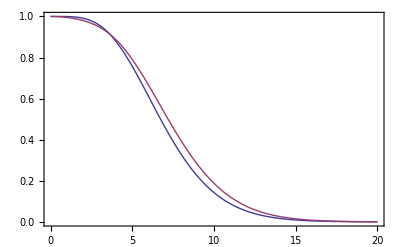

```mathematica
Plot[{F2n[x],F2[x]},{x,0,20},Frame->True]
```

NIntegrate::nlim: x = x is not a valid limit of integration.

General::stop: Further output of NIntegrate :: "nlim" will be suppressed during this calculation.

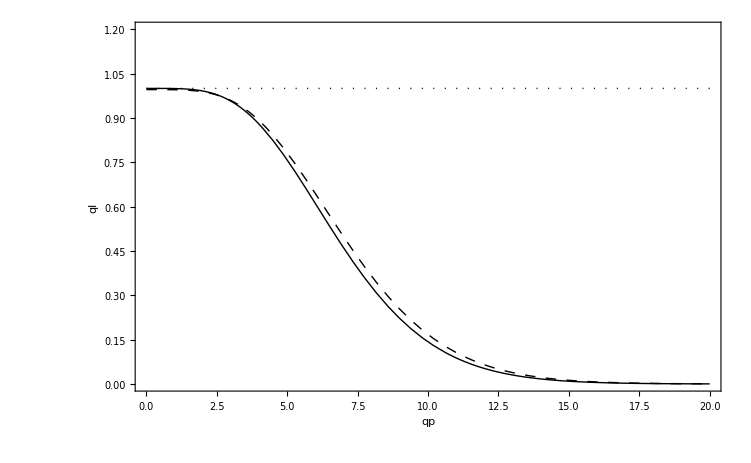

```mathematica
ff1=Plot[{F2n[x],1,F0n[x]},{x,0,20},Frame->True,RotateLabel->False,FrameLabel->{"qp","ql"},PlotRange->{{0,20},{0,1.2}},PlotStyle->{Black,{Black,Dashing[{0.001,0.01}]},{Black,Dashing[{0.01,0.01}]}}]
```

```mathematica
Export["fig11.eps",ff1,"eps"];
```

```mathematica
Qs=(8 π^2 Subscript[Gm, e]^2 Subscript[α, e])/4725(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] (22.68)^2 (0.017)^9
```

1.27554×10^6

```mathematica
NIntegrate[Exp[-z] (z+1) *z^3 (2 PolyLog[3,Exp[z]]-z PolyLog[2,Exp[z]]),{z,0,∞},PrecisionGoal->4]
```

1438.74+2.51319506015487×10^-865 ⅈ

```mathematica
Integrate[Exp[-z] (z+1) *z^3 (2 PolyLog[3,Exp[z]]-z PolyLog[2,Exp[z]]),{z,0,∞}]
```

48 π^2+(14 π^4)/5+(8 π^6)/63+72 (4 ζ(3)+3 ζ(5))

```mathematica
Rsmall[a_]:=(12 Exp[2 a] 1439)/(√π a^(15/2));
```

```mathematica
Rsmall[0.5]
```

4.79387×10^6

```mathematica
vF=.
```

```mathematica
QQ1=(Subscript[Gm, e]^2 Subscript[α, e])/(576 (2 π)^(11/2))(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] 22.68((2 Subscript[α, e] 22.68)/π vF)^(15/4) (((0.34*1000)/22.68)^2+1)^-3(0.02)^(3/2) Exp[-((2 Subscript[α, e] 22.68)/(π (0.02)^2)vF)^(1/2)] R11[1/2((2 Subscript[α, e] 22.68)/(π (0.02)^2) vF)^(1/2)]
```

0.0000771896

```mathematica
QQ10=(Subscript[Gm, e]^2 Subscript[α, e])/(576 (2 π)^(11/2))(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] (1000/4.41)((2 Subscript[α, e](1000/4.41))/π )^(15/4) (((0.34*1000)/(1000/4.41))^2+1)^-3(0.17)^(3/2) Exp[-((2 Subscript[α, e] (1000/4.41))/(π (0.17)^2))^(1/2)]
```

1.19128×10^11

```mathematica
(Subscript[Gm, e]^2 Subscript[α, e])/(576 (2 π)^(11/2))(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] 50((2 Subscript[α, e] 50)/π vF)^(15/4) (((2*28*10^3)/(3*56*50))^2*1.009^6+1)^-3(0.017)^(3/2) Exp[-((2 Subscript[α, e] 50)/(π (0.017)^2) vF)^(1/2)]
```

2.03408×10^-7

```mathematica
(Subscript[Gm, e]^2 Subscript[α, e])/(576 (2 π)^(11/2))(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] 50((2 Subscript[α, e] 50)/π )^(15/4) (((2*28*10^3)/(3*56*50))^2*1.009^6+1)^-3(0.017)^(3/2) Exp[-((2 Subscript[α, e] 50)/(π (0.017)^2))^(1/2)] R11[1/2((2 Subscript[α, e] 50)/(π (0.017)^2))^(1/2)]
```

5.64863×10^-7

From Borisov

```mathematica
1.1912809894784576*^11*((50*4.41*10^13)/10^16)^(43/4)*10^(-3/2)*Exp[-6 ((50*4.41*10^13)/10^16)^(1/2)10] Exp[6]
```

7.71636×10^-8

```mathematica
R11[2.8]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

257.101

```mathematica
R11[1/2((2 Subscript[α, e] (1000/4.41))/(π (0.17)^2) vF)^(1/2)]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

275.32

```mathematica
1/2((2 Subscript[α, e] (1000/4.41))/(π (0.17)^2) vF)^(1/2)
```

2.75641

```mathematica
R11[12]
```

3.90209

```mathematica
R11[1/2((2 Subscript[α, e] 50)/(π (0.017)^2))^(1/2)]
```

3.0986

```mathematica
1/2((2 Subscript[α, e] 50)/(π (0.017)^2)vF)^(1/2)
```

14.1006

```mathematica
vF=√(1-μ1^-2)
```

0.989506

```mathematica
μ1=√(((2*28*10^3)/(3*56*50))^2*1.009^6+1)
```

6.92092

```mathematica
WW1={};a=.;
For[a=0, a≤ 100,WW1=Append[WW1,{a,R12[a]}],a=a+0.5];
```

```mathematica
StandardForm[WW1]
```

```mathematica
WW1={{0.5,4.575134606233091*^6},{1.,56249.42359897693},{1.5,5528.656405796583},{2.,1236.1548458491752},{2.5,426.36054764071224},{3.,191.40910502958945},{3.5,102.35113746411179},{4.,61.88340599891634},{4.5,40.94418677964016},{5.,29.002979097177956},{5.5,21.676087468787557},{6.,16.872360843801005},{6.5,13.593621932467382},{7.,11.259023353935888},{7.5,9.541025158574726},{8.,8.241102638665206},{8.5,7.233884634923544},{9.,6.437580148084291},{9.5,5.7967039804349065},{10.,5.272873941644391},{10.5,4.838849909014236},{11.,4.47483337944216},{11.5,4.166234934478586},{12.,3.902050103810411},{12.5,3.674009227382607},{13.,3.47556882085945},{13.5,3.300748999096806},{14.,3.1476862040064972},{14.5,3.011749722404802},{15.,2.8904013999904348},{15.5,2.7815535811281147},{16.,2.683476494396234},{16.5,2.5947387388598258},{17.,2.5141221579356343},{17.5,2.440615417324892},{18.,2.3733829182927093},{18.5,2.311673171487575},{19.,2.2548738559777406},{19.5,2.20244413923348},{20.,2.153935250788873},{20.5,2.1089389165127224},{21.,2.0671231224415303},{21.5,2.028058545723905},{22.,1.991624085649922},{22.5,1.9574849991369137},{23.,1.9254949028465562},{23.5,1.8954759665816023},{24.,1.8672331083043934},{24.5,1.8406154169366586},{25.,1.8155047155314006},{25.5,1.7917696693915508},{26.,1.7693045653692132},{26.5,1.748157898958331},{27.,1.727821607464554},{27.5,1.7086343568707},{28.,1.6903864683762504},{28.5,1.6730124209672788},{29.,1.6564526383958778},{29.5,1.640652789397836},{30.,1.6255635764436658},{30.5,1.6111402227094407},{31.,1.59732966312517},{31.5,1.584409799280563},{32.,1.5714575598108467},{32.5,1.5593072855063157},{33.,1.5476438727175066},{33.5,1.5364390928055764},{34.,1.5256670950958322},{34.5,1.5146754340447093},{35.,1.5047168337916597},{35.5,1.495118217059977},{36.,1.4858668402180393},{36.5,1.4769464541188353},{37.,1.468337189597445},{37.5,1.4600231879345689},{38.,1.4519786741477057},{38.5,1.4442253321930254},{39.,1.4367248416244103},{39.5,1.429454468505521},{40.,1.4224086177431907},{40.5,1.4155847200604386},{41.,1.4089789808223367},{41.5,1.4025742487289303},{42.,1.3963616356928679},{42.5,1.3903328452321826},{43.,1.3844799517937125},{43.5,1.3787954136641254},{44.,1.3732721952476254},{44.5,1.36789974414976},{45.,1.3626804349937305},{45.5,1.3576069202102443},{46.,1.3526665460275114},{46.5,1.3478535014720587},{47.,1.3431712465866856},{47.5,1.338611043311828},{48.,1.334167384090567},{48.5,1.3298402311569046},{49.,1.3256174504584817},{49.5,1.3214994036986318},{50.,1.3174815919110563},{50.5,1.313573723931118},{51.,1.3097344892924536},{51.5,1.3059981404211756},{52.,1.3023491775767255},{52.5,1.2987844579558983},{53.,1.2953014883291005},{53.5,1.291897411137487},{54.,1.2885695279529263},{54.5,1.285314881468247},{55.,1.2821310177813012},{55.5,1.279016585403634},{56.,1.2759701984905207},{56.5,1.2729873434231862},{57.,1.2700673119065478},{57.5,1.2672080457242403},{58.,1.26440779302794},{58.5,1.2616648085006141},{59.,1.258977056965993},{59.5,1.2563429032244018},{60.,1.2537612736597497},{60.5,1.2512288533324725},{61.,1.2487471099664278},{61.5,1.2463131288134723},{62.,1.2439252659153865},{62.5,1.2415829730337988},{63.,1.239284989534984},{63.5,1.237030474523309},{64.,1.234815970937534},{64.5,1.2326421857583654},{65.,1.2305080072217807},{65.5,1.2284117632190796},{66.,1.2263526064201042},{66.5,1.22432992150798},{67.,1.2223412387042352},{67.5,1.2203897550695435},{68.,1.218470452736129},{68.5,1.216583976362351},{69.,1.2147305764617122},{69.5,1.212906947840206},{70.,1.2111137383411206},{70.5,1.209350162729735},{71.,1.207615338908412},{71.5,1.2059112187372252},{72.,1.2042325443682027},{72.5,1.202580354733831},{73.,1.2009519879319326},{73.5,1.199350416822847},{74.,1.1977749681135572},{74.5,1.1962206395041344},{75.,1.1946969870334592},{75.5,1.1931931962696465},{76.,1.1917123000324314},{76.5,1.1902536930669532},{77.,1.1888168734742761},{77.5,1.1874013747614451},{78.,1.186006694520428},{78.5,1.1846324731250246},{79.,1.1832782223394607},{79.5,1.1819435202273139},{80.,1.1806282858803032},{80.5,1.1793313466265205},{81.,1.1780523671985081},{81.5,1.1767916811464219},{82.,1.175548561159759},{82.5,1.1743235442100841},{83.,1.1731144820474313},{83.5,1.1720422453027606},{84.,1.170864417361193},{84.5,1.1697025666205056},{85.,1.1685543416549045},{85.5,1.1674232148993346},{86.,1.166291379695754},{86.5,1.1652054980224507},{87.,1.164117460944513},{87.5,1.163047263074342},{88.,1.1614244546876045},{88.5,1.160836273414826},{89.,1.159804861151239},{89.5,1.158786573545427},{90.,1.1577810737138348},{90.5,1.1567925452376686},{91.,1.1558069221679614},{91.5,1.154838416540739},{92.,1.1538817869382214},{92.5,1.1529367366809975},{93.,1.152003176541048},{93.5,1.151080891762354},{94.,1.1501696645958752},{94.5,1.1492692954695691},{95.,1.14786621758844},{95.5,1.1470070715680256},{96.,1.146156033083362},{96.5,1.1453156980183061},{97.,1.144485881829475},{97.5,1.143665259275542},{98.,1.1428520858267786},{98.5,1.142046203764008},{99.,1.1412506355798901},{99.5,1.1404626224245658},{100.,1.1396837867572787},{100.5,1.138908483484499}};
```

```mathematica
WW={};a=.;
For[a=0, a≤ 100,WW=Append[WW,{a,R12[a]}],a=a+1];
```

```mathematica
StandardForm[WW]
```

```mathematica
fit0=FindFit[WW1,1+b1/x^(1/2)+b2/x^(3/2)+b3/x^(5/2)+b4/x^(7/2)+b5/x^(9/2)+b6/x^(11/2)+b7/x^(13/2)+b8/x^(15/2),{b1,b2,b3,b4,b5,b6,b7,b8},x]
```

{b1→0.762663,b2→66.875,b3→271.654,b4→2509.36,b5→6754.62,b6→16612.9,b7→19843.8,b8→10188.5}

```mathematica
RR00[x_]:=Evaluate[1+b1/x^(1/2)+b2/x^(3/2)+b3/x^(5/2)+b4/x^(7/2)+b5/x^(9/2)+b6/x^(11/2)+b7/x^(13/2)+b8/x^(15/2)/.fit0];
```

```mathematica
fit1=FindFit[WW1,1+b1/x+b2/x^2+b3/x^3+b4/x^4+b5/x^5+b6/x^6+b7/x^7+b8/x^8,{b1,b2,b3,b4,b5,b6,b7,b8},x]
```

{b1→12.38,b2→154.897,b3→940.615,b4→3991.35,b5→12758.3,b6→16994.7,b7→19298.9,b8→2097.36}

```mathematica
fit=FindFit[WW,1+b1/x+b2/x^2+b3/x^3+b4/x^4+b5/x^5+b6/x^6+b7/x^7+b8/x^8,{b1,b2,b3,b4,b5,b6,b7,b8},x]
```

{b1→12.3067,b2→159.285,b3→866.707,b4→4511.65,b5→10960.5,b6→20170.4,b7→16575.6,b8→2991.93}

```mathematica
RR03[x_]:=Evaluate[1+b1/x+b2/x^2+b3/x^3+b4/x^4+b5/x^5+b6/x^6+b7/x^7+b8/x^8/.fit];
```

```mathematica
RR03[0.1]
```

4.86262×10^11

```mathematica
RR04[x_]:=Evaluate[1+b1/x+b2/x^2+b3/x^3+b4/x^4+b5/x^5+b6/x^6+b7/x^7+b8/x^8/.fit1];
```

```mathematica
RR04[0.1]
```

4.21036×10^11

```mathematica
RR0[x_]:=1+12.31051851979308/x+164.02190802378985/x^2+659.6148639568378/x^3+7407.7961107663505/x^4;
```

```mathematica
RR0[3]
```

139.213

```mathematica
RR02[x_]:=1+13.642039432042798/x+103.98708875652132/x^2+1492.3361564337586/x^3+1509.9444665840804/x^4+18130.135115042045/x^5+11429.17157163479/x^6+21552.21481365898/x^7+1378.4910343514616/x^8;
```

```mathematica
RR02[3]
```

191.367

```mathematica
RR01[x_]:=1+12.31997127803033/x+158.77981871048274/x^2+876.1250707306904/x^3+4421.872662599214/x^4+11342.910538969914/x^5+19550.464119235738/x^6+16843.860636595262/x^7+2406.9729049542193/x^8;
```

```mathematica
RR01[3]
```

191.354

```mathematica
RR=Interpolation[WW, InterpolationOrder->3]
```

InterpolatingFunction[{{1.,101.}},<>]

```mathematica
ListPlot[WW]
```

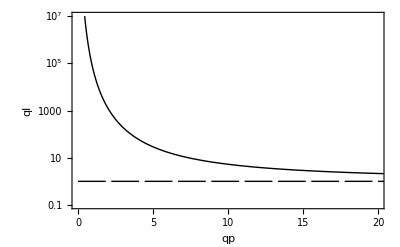

```mathematica
a1=LogPlot[{RR00[x] ,1},{x,0,40},Frame->True,PlotRange->{{0,20},{0.1,10^7}},PlotStyle->{Black,{Black,Dashing[{0.05,0.01}]},{Black,Dashing[{0.005,0.001}]}},RotateLabel->False,FrameLabel->{"qp","ql"}]
```

```mathematica
a1=LogPlot[{RR02[x] ,1},{x,0,40},Frame->True,PlotRange->{{0,40},{0.1,10^4}},PlotStyle->{Black,{Black,Dashing[{0.05,0.01}]},{Black,Dashing[{0.005,0.001}]}},RotateLabel->False,FrameLabel->{"qp","ql"}]
```

```mathematica
Export["fig2.eps",a1,"eps"];
```

## Resonant scattering

```mathematica
Fres1[γ_,η_]:=NIntegrate[(u^3 (1+x) (γ u (1+x) +1-γ u^2 (1-x^2)/2)^2)/(1-Exp[-(1/(u (1-x))-(γ u (1+x))/2-γ) *η/γ])*((1/(u (1-x))-(γ u (1+x))/2-γ)*(1-Exp[-(γ u)/2 (1-x^2)]))/(Exp[η/γ (1/(u (1-x))-(γ u (1-x))/2-γ)]-1),{u,0,∞},{x,-1,1}];
```

```mathematica
Fres1[10^4,10^5]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-2.44942×10^-90

Neutrino synchrotron radiation

```mathematica
Integrate[(ql^2-x) Exp[-x/β],{x,0,ql^2}]
```

β (ql^2+(-1+ⅇ^(-ql^2/β)) β)

```mathematica
μ1=√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)
```

150.847

```mathematica
SynhYaKam[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] NIntegrate[((x+β/μ1^2)^2(1-x) (x-1+Exp[-x]))/(Exp[μ1/t(x+β/μ1^2)]-1),{x,0,1}];
```

```mathematica
SynhYaKam[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

31492.

```mathematica
SynhYaKam0[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] NIntegrate[(x^2(1-x) (x-1+Exp[-x]))/(Exp[μ1/t x]-1),{x,0,1}];
```

```mathematica
SynhYaKam0[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

47634.1

```mathematica
Synh[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] NIntegrate[(x^2(1-x) (x-1+Exp[-x]))/(Exp[μ1/t x]-1),{x,0,1}];
```

```mathematica
Synh[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

47634.1

```mathematica
Synh1[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] NIntegrate[x^2(1-x) (x-1+Exp[-x])Exp[-μ1/t x],{x,0,1}];
```

```mathematica
Synh1[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

45936.9

```mathematica
Synh0[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] (2  t β^2)/μ1^5 Exp[-(√(2 β))/t];
```

```mathematica
Synh0[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

1.33096×10^-35

```mathematica
Synh00[t_,β_,μ1_]:=(4 Subscript[Gm, e]^2 μ1 β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] (12  t^5)/μ1^5;
```

```mathematica
Synh00[0.02,2.27,√(((2*28*10^3)/(3*56*2.27))^2*1.009^6+1)]
```

45977.6

```mathematica
a1=Integrate[x^2(1-x) (x-1+Exp[-x])Exp[-a x],{x,0,1}]
```

(ⅇ^(-a-1) (a^7+2 (3+ⅇ) a^6+(11+20 ⅇ) a^5+12 ⅇ (7+ⅇ^a) a^4-16 ⅇ (-11+2 ⅇ^a) a^3-2 ⅇ (-97+49 ⅇ^a) a^2-12 ⅇ (-9+7 ⅇ^a) a-24 ⅇ (-1+ⅇ^a)))/(a^5 (a+1)^4)

```mathematica
Series[a1,{a,∞,5}]
```

ⅇ^(-a-1) (((1/a)^2+O((1/a)^3))+ⅇ^a (12 ⅇ (1/a)^5+O((1/a)^6)))

```mathematica
a1/.{a->μ1/0.02,b->(√(2*2.27))/μ1}
```

1.4502×10^-58

γ=(√(2eB))/(2T)=(√β)/(√2 t)

```mathematica
Φ1[x_,z_,η_,β_,t_]:=(1+Exp[√(β/(2 t^2))(x-z+1/(x-z))-η])^-1 (1+Exp[√(β/(2 t^2))(x+z-1/(x-z))+η])^-1;
```

```mathematica
Qs0[β_,η_,t_]:=(8 Subscript[Gm, e]^2 √(2 β) β^4)/(3 (2 π)^5)(Subscript[g, V]^2+Subscript[g, A]^2)Subscript[Q, e] NIntegrate[x(x^2-z^2-1+Exp[-(x^2-z^2)])*(Φ1[x,z,η,β,t]+Φ1[x,-z,η,β,t]),{x,1,∞},{z,√(x^2-1),x}];
```

```mathematica
Qs0[100,1,2]
```

9.64281×10^23